```mathematica
Quit[];
```

### metric

```mathematica
$Assumptions={Mp>0,ξ>0};
```

```mathematica
Normal[Series[Sqrt[1+ξ ϕ^2/Mp^2+6 ξ^2 ϕ^2/Mp^2]/(1+ξ ϕ^2/Mp^2),{ϕ,0,2}]]
```

1+((-ξ+6 ξ^2) ϕ^2)/(2 Mp^2)

```mathematica
Integrate[Normal[Series[Sqrt[1+ξ ϕ^2/Mp^2+6 ξ^2 ϕ^2/Mp^2]/(1+ξ ϕ^2/Mp^2),{ϕ,0,2}]],{ϕ,0,ϕJ}]
```

ϕJ+((-ξ+6 ξ^2) ϕJ^3)/(6 Mp^2)

```mathematica
$Assumptions={};
ϕJ[χ_]=ϕJ/.Solve[χ==ϕJ+(6 ξ^2 ϕJ^3)/(6 Mp^2),ϕJ][[1]]
$Assumptions={{Mp>0,ξ>0}};
```

((2/3)^(1/3) Mp^2)/((-9 Mp^2 ξ^4 χ+√3 √(4 Mp^6 ξ^6+27 Mp^4 ξ^8 χ^2))^(1/3))-((-9 Mp^2 ξ^4 χ+√3 √(4 Mp^6 ξ^6+27 Mp^4 ξ^8 χ^2))^(1/3))/(2^(1/3) 3^(2/3) ξ^2)

```mathematica
ϕJs[χ_]=Normal[Series[ϕJ[χ],{χ,0,3}]]//Simplify
```

χ-(ξ^2 χ^3)/Mp^2

```mathematica
Ω2[ϕJ_]=1+ξ ϕJ^2/Mp^2;
```

```mathematica
Normal[Series[-g^2/8 ϕJs[ϵ χ]^2/Ω2[ϕJs[ϵ χ]] ϵ^2 A^2-λ/(4Ω2[ϕJs[ϵ χ]])ϕJs[ϵ χ]^4,{ϵ,0,6}]]/.{ϵ->1}//Expand
```

-1/8 A^2 g^2 χ^2-(λ χ^4)/4+(A^2 g^2 ξ χ^4)/(8 Mp^2)+(A^2 g^2 ξ^2 χ^4)/(4 Mp^2)+(λ ξ χ^6)/(4 Mp^2)+(λ ξ^2 χ^6)/Mp^2

#### field-space curvature

```mathematica
Quit[];
```

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord]
```

4

```mathematica
metric=DiagonalMatrix[Table[1/(1+ξ Sum[coord[[i]]^2/Mp^2,{i,n}]),{j,n}]]+Table[(6 ξ^2 coord[[i]]coord[[j]]/Mp^2)/((1+ξ Sum[coord[[k]]^2/Mp^2,{k,n}])^2),{i,n},{j,n}]//Simplify
```

{{(Mp^4+Mp^2 ξ (h2^2+h3^2+h4^2+h1^2 (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h1 h2 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h1 h3 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h1 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)},{(6 h1 h2 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(Mp^4+Mp^2 ξ (h1^2+h2^2+h3^2+h4^2+6 h2^2 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h2 h3 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h2 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)},{(6 h1 h3 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h2 h3 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(Mp^4+Mp^2 ξ (h1^2+h2^2+h3^2+h4^2+6 h3^2 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h3 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)},{(6 h1 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h2 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(6 h3 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2),(Mp^4+Mp^2 ξ (h1^2+h2^2+h3^2+h4^2+6 h4^2 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)}}

```mathematica
metric//MatrixForm
```

((Mp^4+Mp^2 ξ (h2^2+h3^2+h4^2+h1^2 (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h1 h2 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h1 h3 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h1 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
(6 h1 h2 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (Mp^4+Mp^2 ξ (h1^2+h2^2+h3^2+h4^2+6 h2^2 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h2 h3 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h2 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
(6 h1 h3 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h2 h3 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (Mp^4+Mp^2 ξ (h1^2+h2^2+h3^2+h4^2+6 h3^2 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h3 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
(6 h1 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h2 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (6 h3 h4 Mp^2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2) | (Mp^4+Mp^2 ξ (h1^2+h2^2+h3^2+h4^2+6 h4^2 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2))

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+ξ (h1^2+(h2^2+h3^2+h4^2) (1+6 ξ))))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),-(6 h1 h2 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),-(6 h1 h3 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),-(6 h1 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ))},{-(6 h1 h2 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+ξ (h2^2+h1^2 (1+6 ξ)+(h3^2+h4^2) (1+6 ξ))))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),-(6 h2 h3 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),-(6 h2 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ))},{-(6 h1 h3 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),-(6 h2 h3 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+ξ (h2^2+h3^2+h4^2+6 h2^2 ξ+6 h4^2 ξ+h1^2 (1+6 ξ))))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),-(6 h3 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ))},{-(6 h1 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),-(6 h2 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),-(6 h3 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)),((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+ξ (h2^2+h3^2+h4^2+6 h2^2 ξ+6 h3^2 ξ+h1^2 (1+6 ξ))))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ))}}

```mathematica
inversemetric//MatrixForm
```

(((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+ξ (h1^2+(h2^2+h3^2+h4^2) (1+6 ξ))))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | -(6 h1 h2 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | -(6 h1 h3 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | -(6 h1 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ))
-(6 h1 h2 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | ((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+ξ (h2^2+h1^2 (1+6 ξ)+(h3^2+h4^2) (1+6 ξ))))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | -(6 h2 h3 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | -(6 h2 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ))
-(6 h1 h3 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | -(6 h2 h3 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | ((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+ξ (h2^2+h3^2+h4^2+6 h2^2 ξ+6 h4^2 ξ+h1^2 (1+6 ξ))))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | -(6 h3 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ))
-(6 h1 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | -(6 h2 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | -(6 h3 h4 ξ^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)) | ((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+ξ (h2^2+h3^2+h4^2+6 h2^2 ξ+6 h3^2 ξ+h1^2 (1+6 ξ))))/(Mp^4+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | -(h1 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[1, 2, 1] | -(h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 2, 2] | (h1 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[1, 3, 1] | -(h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 3, 3] | (h1 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[1, 4, 1] | -(h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 4, 4] | (h1 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[2, 1, 1] | (h2 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[2, 2, 1] | -(h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 2, 2] | -(h2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[2, 3, 2] | -(h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 3, 3] | (h2 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[2, 4, 2] | -(h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 4, 4] | (h2 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[3, 1, 1] | (h3 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[3, 2, 2] | (h3 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[3, 3, 1] | -(h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 3, 2] | -(h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 3, 3] | -(h3 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[3, 4, 3] | -(h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 4, 4] | (h3 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[4, 1, 1] | (h4 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[4, 2, 2] | (h4 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[4, 3, 3] | (h4 ξ (1+6 ξ))/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[4, 4, 1] | -(h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 2] | -(h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 3] | -(h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 4] | -(h4 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 1, 2, 1] | -(12 h1 h2 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[1, 1, 3, 1] | -(12 h1 h3 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[1, 1, 4, 1] | -(12 h1 h4 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[1, 2, 2, 1] | ξ ((3 h2^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)-1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)+(2 ξ (h1+6 h1 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))-(h1^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h3^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h4^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h1^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h2^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[1, 2, 3, 1] | (h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 3, 2] | -(h1 h3 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[1, 2, 4, 1] | (h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 4, 2] | -(h1 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[1, 3, 2, 1] | (h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 3, 1] | ξ ((3 h3^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)-1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)+(2 ξ (h1+6 h1 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))-(h1^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h2^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h4^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h1^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h3^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[1, 3, 3, 2] | (h1 h2 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[1, 3, 4, 1] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 4, 3] | -(h1 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[1, 4, 2, 1] | (h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 3, 1] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 4, 1] | ξ ((3 h4^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)-1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)+(2 ξ (h1+6 h1 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))-(h1^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h2^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h3^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h1^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h4^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[1, 4, 4, 2] | (h1 h2 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[1, 4, 4, 3] | (h1 h3 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[2, 1, 2, 1] | ξ (-(3 h1^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)+1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)-(2 ξ (h2+6 h2 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))+(h2^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h3^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h4^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h2^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[2, 1, 3, 1] | -(h2 h3 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[2, 1, 3, 2] | (h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 4, 1] | -(h2 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[2, 1, 4, 2] | (h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 2, 2, 1] | (12 h1 h2 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[2, 2, 3, 2] | -(12 h2 h3 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[2, 2, 4, 2] | -(12 h2 h4 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[2, 3, 2, 1] | -(h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 3, 1] | (h1 h2 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[2, 3, 3, 2] | ξ ((3 h3^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)-1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)+(2 ξ (h2+6 h2 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))+(h1^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h2^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h4^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h2^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h3^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[2, 3, 4, 2] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 4, 3] | -(h2 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[2, 4, 2, 1] | -(h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 3, 2] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 4, 1] | (h1 h2 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[2, 4, 4, 2] | ξ ((3 h4^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)-1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)+(2 ξ (h2+6 h2 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))+(h1^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h2^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h3^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h2^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h4^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[2, 4, 4, 3] | (h2 h3 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 1, 2, 1] | -(h2 h3 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 1, 3, 1] | ξ (-(3 h1^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)+1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)-(2 ξ (h3+6 h3 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))-(h2^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h3^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h4^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h3^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[3, 1, 3, 2] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 4, 1] | -(h3 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 1, 4, 3] | (h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 2, 1] | (h1 h3 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 2, 3, 1] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 3, 2] | ξ (-(3 h2^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)+1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)-(2 ξ (h3+6 h3 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))-(h1^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h3^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h4^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h3^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[3, 2, 4, 2] | -(h3 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 2, 4, 3] | (h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 3, 3, 1] | (12 h1 h3 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 3, 3, 2] | (12 h2 h3 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 3, 4, 3] | -(12 h3 h4 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 4, 3, 1] | -(h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 3, 2] | -(h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 4, 1] | (h1 h3 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 4, 4, 2] | (h2 h3 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 4, 4, 3] | ξ ((3 h4^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)-1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)+(2 ξ (h3+6 h3 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))+(h1^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h2^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h3^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h3^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h4^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[4, 1, 2, 1] | -(h2 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 1, 3, 1] | -(h3 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 1, 4, 1] | ξ (-(3 h1^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)+1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)-(2 ξ (h4+6 h4 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))-(h2^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h3^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h4^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h4^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[4, 1, 4, 2] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 4, 3] | -(h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 2, 1] | (h1 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 2, 3, 2] | -(h3 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 2, 4, 1] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 4, 2] | ξ (-(3 h2^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)+1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)-(2 ξ (h4+6 h4 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))-(h1^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h3^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h4^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h4^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[4, 2, 4, 3] | -(h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 3, 1] | (h1 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 3, 3, 2] | (h2 h4 ξ^2 (1+6 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 3, 4, 1] | -(h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 4, 2] | -(h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 4, 3] | ξ (-(3 h3^2 ξ)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)+1/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)-(2 ξ (h4+6 h4 ξ)^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(1+6 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))-(h1^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h2^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h4^2 ξ (1+6 ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(h4^2 ξ (1+6 ξ) (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h3^2 ξ (Mp^2 (1-6 ξ)+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))))
R[4, 4, 4, 1] | (12 h1 h4 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 4, 4, 2] | (12 h2 h4 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 4, 4, 3] | (12 h3 h4 ξ^3 (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | (2 ξ ((h2^2+h3^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^3 (1+6 ξ)^2+Mp^6 (3+9 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ^2 (1+6 ξ) (3 h1^2 (1+6 ξ)+(h2^2+h3^2+h4^2) (5+12 ξ))+Mp^4 ξ ((h2^2+h3^2+h4^2) (7+39 ξ+36 ξ^2)+h1^2 (6+45 ξ+54 ξ^2))))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[2, 1] | (2 h1 h2 ξ^2 (-1+(6 ξ (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 2] | (2 ξ ((h1^2+h3^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^3 (1+6 ξ)^2+Mp^6 (3+9 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ^2 (1+6 ξ) (3 h2^2 (1+6 ξ)+h1^2 (5+12 ξ)+(h3^2+h4^2) (5+12 ξ))+Mp^4 ξ (h1^2 (7+39 ξ+36 ξ^2)+(h3^2+h4^2) (7+39 ξ+36 ξ^2)+h2^2 (6+45 ξ+54 ξ^2))))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 1] | (2 h1 h3 ξ^2 (-1+(6 ξ (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2] | (2 h2 h3 ξ^2 (-1+(6 ξ (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 3] | (2 ξ ((h1^2+h2^2+h4^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^3 (1+6 ξ)^2+Mp^6 (3+9 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ^2 (1+6 ξ) (3 h3^2+5 h4^2+18 h3^2 ξ+12 h4^2 ξ+h1^2 (5+12 ξ)+h2^2 (5+12 ξ))+Mp^4 ξ (6 h3^2+7 h4^2+45 h3^2 ξ+39 h4^2 ξ+54 h3^2 ξ^2+36 h4^2 ξ^2+h1^2 (7+39 ξ+36 ξ^2)+h2^2 (7+39 ξ+36 ξ^2))))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 1] | (2 h1 h4 ξ^2 (-1+(6 ξ (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2] | (2 h2 h4 ξ^2 (-1+(6 ξ (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3] | (2 h3 h4 ξ^2 (-1+(6 ξ (Mp^4 (1+3 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ (1+6 ξ)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 4] | (2 ξ ((h1^2+h2^2+h3^2) (h1^2+h2^2+h3^2+h4^2)^2 ξ^3 (1+6 ξ)^2+Mp^6 (3+9 ξ)+(h1^2+h2^2+h3^2+h4^2) Mp^2 ξ^2 (1+6 ξ) (5 h3^2+3 h4^2+12 h3^2 ξ+18 h4^2 ξ+h1^2 (5+12 ξ)+h2^2 (5+12 ξ))+Mp^4 ξ (7 h3^2+6 h4^2+39 h3^2 ξ+45 h4^2 ξ+36 h3^2 ξ^2+54 h4^2 ξ^2+h1^2 (7+39 ξ+36 ξ^2)+h2^2 (7+39 ξ+36 ξ^2))))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]/.{h1^2->h^2-h2^2-h3^2-h4^2,h1^4->(h^2-h2^2-h3^2-h4^2)^2}//FullSimplify
```

(6 ξ (4 Mp^4 (1+3 ξ)+h^4 ξ^2 (1+6 ξ)^2+h^2 Mp^2 ξ (1+6 ξ) (5+6 ξ)))/((Mp^3+h^2 Mp ξ (1+6 ξ))^2)

```mathematica
scalar-6ξ(4+12ξ+(5ξ+36 ξ^2+36 ξ^3)h^2/Mp^2+ξ^2(1+6ξ)^2 h^4/Mp^4)/(Mp^2(1+ξ(1+6ξ)h^2/Mp^2)^2)//Simplify
```

0

#### embedding

```mathematica
Quit[]
```

```mathematica
$Assumptions={ξ>0,r>0,ρ>0,ρ2>0,z>0,ξ ρ^2<1,ξ ρ2<1,xr2<1,sqxr<1};
```

```mathematica
F[r_]=Sqrt[1+ξ(6ξ+1)r^2]/(1+ξ r^2);
ρ[r_]=r/Sqrt[1+ξ r^2];
```

```mathematica
dzdr[r_]=Sqrt[F[r]^2-ρ'[r]^2]//Simplify
```

√((r^2 ξ (2+(6+r^2) ξ+6 r^2 ξ^2))/((1+r^2 ξ)^3))

```mathematica
dzdr[0]
```

0

```mathematica
Normal[Series[dzdr[r],{r,∞,1}]]
```

(√(ξ (ξ+6 ξ^2)))/(r ξ^(3/2))

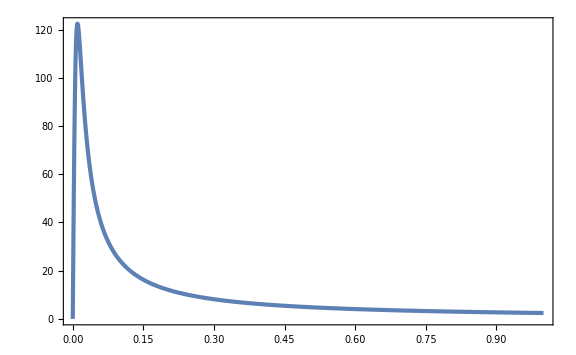

```mathematica
Plot[dzdr[r]/.{ξ->10^4},{r,0,1},PlotRange->Full]
```

```mathematica
z[r_]=Integrate[dzdr[rp],{rp,0,r}]
```

(√(2+6 ξ)-√(1+6 ξ+1/(1+r^2 ξ))+√(1+6 ξ) (-ArcSinh[√(1+6 ξ)]+ArcSinh[√((1+6 ξ) (1+r^2 ξ))]))/(√ξ)

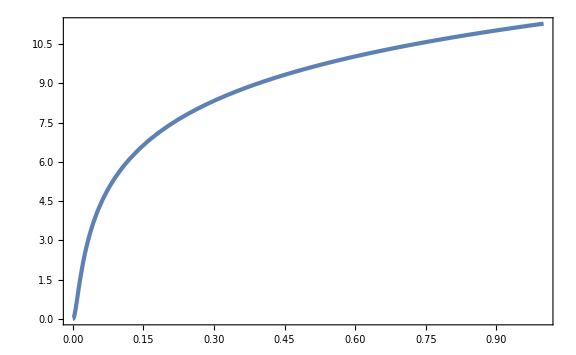

```mathematica
Plot[z[r]/.{ξ->10^4},{r,0,1}]
```

```mathematica
r[ρ_]=ρ/Sqrt[1-ξ ρ^2];
```

```mathematica
ρ[r[ρ]]//Simplify
```

ρ

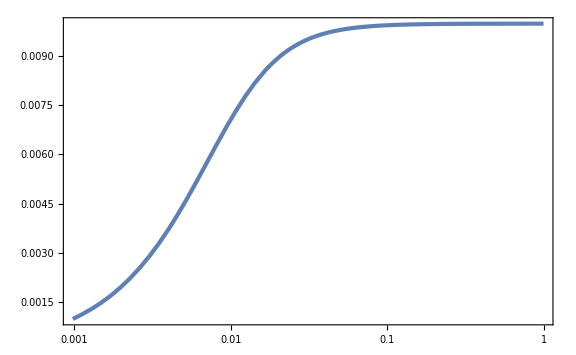

```mathematica
LogLinearPlot[ρ[r]/.{ξ->10^4},{r,0,1},PlotRange->Full]
```

```mathematica
z[0]
```

0

```mathematica
zinρ2[ρ2_]=z[r[Sqrt[ρ2]]]//FullSimplify
```

(√(2+6 ξ)-√(2-ξ (-6+ρ2))+√(1+6 ξ) (-ArcSinh[√(1+6 ξ)]+ArcSinh[√((1+6 ξ)/(1-ξ ρ2))]))/(√ξ)

```mathematica
zinρ2[ρ2]-1/Sqrt[ξ](Sqrt[6ξ+1](ArcSinh[Sqrt[(6ξ+1)/(1-ξ ρ2)]]-ArcSinh[Sqrt[6ξ+1]])-Sqrt[6ξ+1+1-ξ ρ2]+Sqrt[6ξ+2])//Simplify
```

0

```mathematica
Normal[Series[Simplify[Normal[Series[Sqrt[ξ/(6ξ+1)]zinρ2[(1-ϵ)/ξ],{ϵ,0,0}]],{ϵ>0}],{ξ,∞,0}]]/.{ϵ->1-ξ ρ2}
```

-1/2 Log[1-ξ ρ2]

```mathematica
ρ2inzasym[zz_]=1/ξ(1-Exp[-2Sqrt[ξ/(6ξ+1)]zz])
```

(1-ⅇ^(-2 zz √(ξ/(1+6 ξ))))/ξ

```mathematica
Collect[Normal[Series[(ϵ^2 ρ^2-ρ2inzasym[ϵ z])^2,{ϵ,0,6},{ξ,∞,2}]]/.{ϵ->1},{z,ρ}]
```

-(√(2/3) z^5)/(9 ξ^2)+(31 z^6)/(1215 ξ^2)+z (1/(3 √6 ξ^2)-(2 √(2/3))/ξ) ρ^2+ρ^4+z^4 (7/(27 ξ^2)+(-1/(81 ξ^2)+1/(27 ξ)) ρ^2)+z^2 (2/(3 ξ^2)+(-1/(9 ξ^2)+2/(3 ξ)) ρ^2)+z^3 (-(2 √(2/3))/(3 ξ^2)+(1/(9 √6 ξ^2)-(2 √(2/3))/(9 ξ)) ρ^2)

```mathematica
dρ2dz[ρ2_]=(zinρ2'[ρ2])^-1//Simplify
d2ρ2dz2[ρ2_]=(zinρ2'[ρ2])^-1 dρ2dz'[ρ2]//Simplify
d3ρ2dz3[ρ2_]=(zinρ2'[ρ2])^-1 d2ρ2dz2'[ρ2]//Simplify
d4ρ2dz4[ρ2_]=(zinρ2'[ρ2])^-1 d3ρ2dz3'[ρ2]//Simplify
d5ρ2dz5[ρ2_]=(zinρ2'[ρ2])^-1 d4ρ2dz4'[ρ2]//Simplify
d6ρ2dz6[ρ2_]=(zinρ2'[ρ2])^-1 d5ρ2dz5'[ρ2]//Simplify
d7ρ2dz7[ρ2_]=(zinρ2'[ρ2])^-1 d6ρ2dz6'[ρ2]//Simplify
d8ρ2dz8[ρ2_]=(zinρ2'[ρ2])^-1 d7ρ2dz7'[ρ2]//Simplify
```

(2-2 ξ ρ2)/(√(ξ (2-ξ (-6+ρ2))))

-(2 (-3+ξ (-12+ρ2)) (-1+ξ ρ2))/(-2+ξ (-6+ρ2))^2

-(8 √ξ (1+6 ξ)^2 (-1+ξ ρ2))/(2-ξ (-6+ρ2))^(7/2)

(8 ξ (1+6 ξ)^2 (-1+ξ ρ2) (-3+ξ (12+5 ρ2)))/(2-ξ (-6+ρ2))^5

-(16 ξ^(3/2) (1+6 ξ)^2 (-1+ξ ρ2) (-1-12 ξ (7+ρ2)+3 ξ^2 (24+36 ρ2+5 ρ2^2)))/(2-ξ (-6+ρ2))^(13/2)

1/(-2+ξ (-6+ρ2))^8 16 ξ^2 (1+6 ξ)^2 (-1+ξ ρ2) (57+ξ (456-95 ρ2)-3 ξ^2 (984+632 ρ2+21 ρ2^2)+3 ξ^3 (288+1128 ρ2+504 ρ2^2+35 ρ2^3))

-1/(2-ξ (-6+ρ2))^(19/2)128 ξ^(5/2) (1+6 ξ)^2 (-1+ξ ρ2) (-38+6 ξ (82+39 ρ2)+ξ^2 (6264+612 ρ2-300 ρ2^2)-72 ξ^3 (150+249 ρ2+50 ρ2^2)+3 ξ^4 (432+3888 ρ2+3960 ρ2^2+840 ρ2^3+35 ρ2^4))

-1/(-2+ξ (-6+ρ2))^11 128 ξ^3 (1+6 ξ)^2 (-1+ξ ρ2) (-366-4 ξ (3273+88 ρ2)+6 ξ^2 (-3948+7412 ρ2+735 ρ2^2)-36 ξ^3 (-11268-7608 ρ2+585 ρ2^2+155 ρ2^3)+27 ξ^4 (-10704-37184 ρ2-19440 ρ2^2-1640 ρ2^3+35 ρ2^4)+27 ξ^5 (576+11184 ρ2+22320 ρ2^2+10200 ρ2^3+1260 ρ2^4+35 ρ2^5))

```mathematica
ρ2inz[z_]=dρ2dz[0]z+1/2 d2ρ2dz2[0] z^2+1/(2 3)d3ρ2dz3[0] z^3+1/(2 3 4)d4ρ2dz4[0] z^4+1/(2 3 4 5)d5ρ2dz5[0] z^5+1/(2 3 4 5 6)d6ρ2dz6[0] z^6+1/(2 3 4 5 6 7)d7ρ2dz7[0] z^7+1/(2 3 4 5 6 7 8)d8ρ2dz8[0] z^8
```

(z^2 (-3-12 ξ))/(-2-6 ξ)^2+(4 z^3 √ξ (1+6 ξ)^2)/(3 (2+6 ξ)^(7/2))+(2 z)/(√(ξ (2+6 ξ)))-(z^4 ξ (1+6 ξ)^2 (-3+12 ξ))/(3 (2+6 ξ)^5)+(2 z^5 ξ^(3/2) (1+6 ξ)^2 (-1-84 ξ+72 ξ^2))/(15 (2+6 ξ)^(13/2))-(z^6 ξ^2 (1+6 ξ)^2 (57+456 ξ-2952 ξ^2+864 ξ^3))/(45 (-2-6 ξ)^8)+(8 z^7 ξ^(5/2) (1+6 ξ)^2 (-38+492 ξ+6264 ξ^2-10800 ξ^3+1296 ξ^4))/(315 (2+6 ξ)^(19/2))+(z^8 ξ^3 (1+6 ξ)^2 (-366-13092 ξ-23688 ξ^2+405648 ξ^3-289008 ξ^4+15552 ξ^5))/(315 (-2-6 ξ)^11)

```mathematica
Collect[Normal[Series[Normal[Series[zinρ2[ρ2],{ρ2,0,8}]]/.{ρ2->ρ2inz[z]},{z,0,8}]],z,FullSimplify]
```

z

```mathematica
Collect[Normal[Series[(ϵ^2 ρ^2-ρ2inz[ϵ z])^2,{ϵ,0,6},{ξ,∞,2}]]/.{ϵ->1},{z,ρ}]
```

-(√(2/3) z^5)/(9 ξ^2)+(31 z^6)/(1215 ξ^2)+z ((√(2/3))/(3 ξ^2)-(2 √(2/3))/ξ) ρ^2+ρ^4+z^4 (7/(27 ξ^2)+(-19/(324 ξ^2)+1/(27 ξ)) ρ^2)+z^2 (2/(3 ξ^2)+(-5/(18 ξ^2)+2/(3 ξ)) ρ^2)+z^3 (-(2 √(2/3))/(3 ξ^2)+((5 √(2/3))/(27 ξ^2)-(2 √(2/3))/(9 ξ)) ρ^2)

### Palatini

```mathematica
$Assumptions={Mp>0,ξ>0};
```

```mathematica
$Assumptions={};
Simplify[Integrate[1/Sqrt[1+ξ ϕ^2/Mp^2],{ϕ,0,ϕJ}],{Mp>0,ξ>0,ϕJ>0}]
$Assumptions={Mp>0,ξ>0};
```

(Mp ArcSinh[(√ξ ϕJ)/Mp])/(√ξ)

```mathematica
ϕJ[χ_]=Mp/Sqrt[ξ] Sinh[Sqrt[ξ] χ/Mp];
```

```mathematica
ϕJs[χ_]=Normal[Series[ϕJ[χ],{χ,0,3}]]//Simplify
```

χ+(ξ χ^3)/(6 Mp^2)

```mathematica
Ω2[ϕJ_]=1+ξ ϕJ^2/Mp^2;
```

```mathematica
Normal[Series[-g^2/8 ϕJ[ϵ χ]^2/Ω2[ϕJ[ϵ χ]] ϵ^2 A^2-λ/(4Ω2[ϕJ[ϵ χ]])ϕJ[ϵ χ]^4,{ϵ,0,6}]]/.{ϵ->1}//Expand
```

-1/8 A^2 g^2 χ^2-(λ χ^4)/4+(A^2 g^2 ξ χ^4)/(12 Mp^2)+(λ ξ χ^6)/(12 Mp^2)

#### field-space curvature

```mathematica
Quit[]
```

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord]
```

4

```mathematica
metric=DiagonalMatrix[Table[1/(1+ξ Sum[coord[[i]]^2/Mp^2,{i,n}]),{j,n}]]//Simplify
```

{{Mp^2/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ),0,0,0},{0,Mp^2/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ),0,0},{0,0,Mp^2/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ),0},{0,0,0,Mp^2/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)}}

```mathematica
metric//MatrixForm
```

(Mp^2/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) | 0 | 0 | 0
0 | Mp^2/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) | 0 | 0
0 | 0 | Mp^2/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ) | 0
0 | 0 | 0 | Mp^2/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ))

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{1+((h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2,0,0,0},{0,1+((h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2,0,0},{0,0,1+((h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2,0},{0,0,0,1+((h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2}}

```mathematica
inversemetric//MatrixForm
```

(1+((h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2 | 0 | 0 | 0
0 | 1+((h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2 | 0 | 0
0 | 0 | 1+((h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2 | 0
0 | 0 | 0 | 1+((h1^2+h2^2+h3^2+h4^2) ξ)/Mp^2)

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | -(h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 2, 1] | -(h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 2, 2] | (h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 3, 1] | -(h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 3, 3] | (h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 4, 1] | -(h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[1, 4, 4] | (h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 1, 1] | (h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 2, 1] | -(h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 2, 2] | -(h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 3, 2] | -(h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 3, 3] | (h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 4, 2] | -(h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[2, 4, 4] | (h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 1, 1] | (h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 2, 2] | (h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 3, 1] | -(h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 3, 2] | -(h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 3, 3] | -(h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 4, 3] | -(h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[3, 4, 4] | (h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 1, 1] | (h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 2, 2] | (h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 3, 3] | (h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 1] | -(h1 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 2] | -(h2 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 3] | -(h3 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)
Γ[4, 4, 4] | -(h4 ξ)/(Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 2, 2, 1] | -(ξ (2 Mp^2+(h3^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 3, 1] | (h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 3, 2] | -(h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 4, 1] | (h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 2, 4, 2] | -(h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 2, 1] | (h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 3, 1] | -(ξ (2 Mp^2+(h2^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 3, 2] | (h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 4, 1] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 3, 4, 3] | -(h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 2, 1] | (h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 3, 1] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 4, 1] | -(ξ (2 Mp^2+(h2^2+h3^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 4, 2] | (h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[1, 4, 4, 3] | (h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 2, 1] | (ξ (2 Mp^2+(h3^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 3, 1] | -(h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 3, 2] | (h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 4, 1] | -(h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1, 4, 2] | (h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 2, 1] | -(h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 3, 1] | (h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 3, 2] | -(ξ (2 Mp^2+(h1^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 4, 2] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 3, 4, 3] | -(h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 2, 1] | -(h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 3, 2] | (h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 4, 1] | (h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 4, 2] | -(ξ (2 Mp^2+(h1^2+h3^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 4, 4, 3] | (h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 2, 1] | -(h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 3, 1] | (ξ (2 Mp^2+(h2^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 3, 2] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 4, 1] | -(h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1, 4, 3] | (h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 2, 1] | (h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 3, 1] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 3, 2] | (ξ (2 Mp^2+(h1^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 4, 2] | -(h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2, 4, 3] | (h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 3, 1] | -(h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 3, 2] | -(h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 4, 1] | (h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 4, 2] | (h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 4, 4, 3] | -(ξ (2 Mp^2+(h1^2+h2^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 2, 1] | -(h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 3, 1] | -(h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 4, 1] | (ξ (2 Mp^2+(h2^2+h3^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 4, 2] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1, 4, 3] | -(h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 2, 1] | (h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 3, 2] | -(h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 4, 1] | -(h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 4, 2] | (ξ (2 Mp^2+(h1^2+h3^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2, 4, 3] | -(h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 3, 1] | (h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 3, 2] | (h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 4, 1] | -(h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 4, 2] | -(h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3, 4, 3] | (ξ (2 Mp^2+(h1^2+h2^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | (2 ξ (3 Mp^2+(h2^2+h3^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 1] | -(2 h1 h2 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[2, 2] | (2 ξ (3 Mp^2+(h1^2+h3^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 1] | -(2 h1 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 2] | -(2 h2 h3 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[3, 3] | (2 ξ (3 Mp^2+(h1^2+h2^2+h4^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 1] | -(2 h1 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 2] | -(2 h2 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 3] | -(2 h3 h4 ξ^2)/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)
R[4, 4] | (2 ξ (3 Mp^2+(h1^2+h2^2+h3^2) ξ))/((Mp^2+(h1^2+h2^2+h3^2+h4^2) ξ)^2)

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]/.{h1^2->h^2-h2^2-h3^2-h4^2,h1^4->(h^2-h2^2-h3^2-h4^2)^2}//FullSimplify
```

(6 ξ (4 Mp^2+h^2 ξ))/(Mp^4+h^2 Mp^2 ξ)

#### embedding

```mathematica
Quit[]
```

```mathematica
$Assumptions={ξ>0,r>0,ρ>0,ρ2>0,z>0,ξ ρ^2<1,ξ ρ2<1,xr2<1,sqxr<1};
```

```mathematica
F[r_]=1/Sqrt[1+ξ r^2];
ρ[r_]=r/Sqrt[1+ξ r^2];
```

```mathematica
dzdr[r_]=Sqrt[F[r]^2-ρ'[r]^2]//Simplify
```

√((r^2 ξ (2+r^2 ξ))/((1+r^2 ξ)^3))

```mathematica
dzdr[0]
```

0

```mathematica
Normal[Series[dzdr[r],{r,∞,1}]]
```

1/(r √ξ)

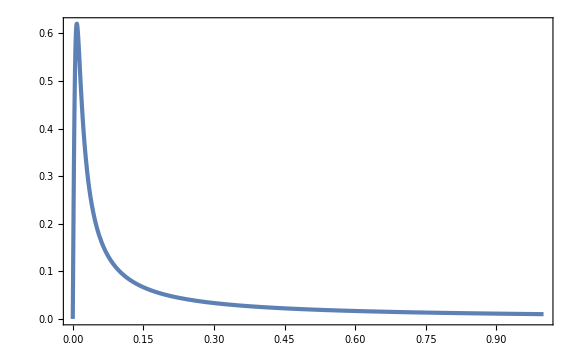

```mathematica
Plot[dzdr[r]/.{ξ->10^4},{r,0,1},PlotRange->Full]
```

```mathematica
z[r_]=Integrate[dzdr[rp],{rp,0,r}]//Simplify
```

(2 √2-2 √((2+r^2 ξ)/(1+r^2 ξ))+Log[((-3+2 √2) (1+√((1+r^2 ξ)/(2+r^2 ξ))))/(-1+√((1+r^2 ξ)/(2+r^2 ξ)))])/(2 √ξ)

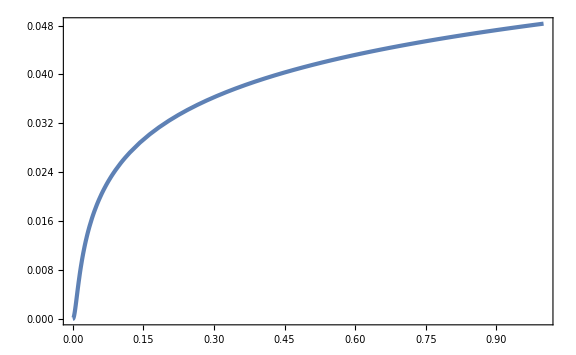

```mathematica
Plot[z[r]/.{ξ->10^4},{r,0,1}]
```

```mathematica
r[ρ_]=ρ/Sqrt[1-ξ ρ^2];
```

```mathematica
ρ[r[ρ]]//Simplify
```

ρ

```mathematica
LogLinearPlot[ρ[r]/.{ξ->10^4},{r,0,1},PlotRange->Full]
```

-Graphics-

```mathematica
z[0]//Simplify
```

0

```mathematica
zinρ2[ρ2_]=z[r[Sqrt[ρ2]]]//FullSimplify
```

(2 √2-2 √(2-ξ ρ2)+Log[3-2 √2]-Log[-1+√(2-ξ ρ2)]+Log[1+√(2-ξ ρ2)])/(2 √ξ)

```mathematica
zinρ2[ρ2]-1/Sqrt[ξ](Sqrt[2]-Sqrt[2-ξ ρ2]-ArcSinh[1]+ArcSinh[Sqrt[1/(1-ξ ρ2)]])//TrigToExp//FullSimplify
```

0

```mathematica
Normal[Series[Simplify[Normal[Series[Sqrt[ξ]zinρ2[(1-ϵ)/ξ],{ϵ,0,0}]],{ϵ>0}],{ξ,∞,0}]]/.{ϵ->1-ξ ρ2}
```

-1+√2+Log[2]+1/2 Log[3-2 √2]-1/2 Log[1-ξ ρ2]

```mathematica
Sinh[x]^2//TrigToExp
```

-1/2+ⅇ^(-2 x)/4+ⅇ^(2 x)/4

```mathematica
ρ2inzasym[zz_]=1/ξ(1-4Exp[-2Sqrt[ξ]zz])
```

(1-4 ⅇ^(-2 zz √ξ))/ξ

```mathematica
Collect[Normal[Series[(ϵ^2 ρ^2-ρ2inzasym[ϵ z])^2,{ϵ,0,6},{ξ,∞,2}]]/.{ϵ->1},{z,ρ}]
```

9/ξ^2-(672 z^5 √ξ)/5+(4064 z^6 ξ)/45+(6 ρ^2)/ξ+ρ^4+z^2 (112/ξ+16 ρ^2)+z (-48/ξ^(3/2)-(16 ρ^2)/(√ξ))+z^3 (-160/(√ξ)-(32 √ξ ρ^2)/3)+z^4 (496/3+(16 ξ ρ^2)/3)

```mathematica
dρ2dz[ρ2_]=(zinρ2'[ρ2])^-1//Simplify
d2ρ2dz2[ρ2_]=(zinρ2'[ρ2])^-1 dρ2dz'[ρ2]//Simplify
d3ρ2dz3[ρ2_]=(zinρ2'[ρ2])^-1 d2ρ2dz2'[ρ2]//Simplify
d4ρ2dz4[ρ2_]=(zinρ2'[ρ2])^-1 d3ρ2dz3'[ρ2]//Simplify
d5ρ2dz5[ρ2_]=(zinρ2'[ρ2])^-1 d4ρ2dz4'[ρ2]//Simplify
d6ρ2dz6[ρ2_]=(zinρ2'[ρ2])^-1 d5ρ2dz5'[ρ2]//Simplify
d7ρ2dz7[ρ2_]=(zinρ2'[ρ2])^-1 d6ρ2dz6'[ρ2]//Simplify
d8ρ2dz8[ρ2_]=(zinρ2'[ρ2])^-1 d7ρ2dz7'[ρ2]//Simplify
```

(2-2 ξ ρ2)/(√(ξ (2-ξ ρ2)))

-(2 (3-4 ξ ρ2+ξ^2 ρ2^2))/(-2+ξ ρ2)^2

-(8 √ξ (-1+ξ ρ2))/(2-ξ ρ2)^(7/2)

-(8 ξ (3-8 ξ ρ2+5 ξ^2 ρ2^2))/(-2+ξ ρ2)^5

-(16 ξ^(3/2) (1+11 ξ ρ2-27 ξ^2 ρ2^2+15 ξ^3 ρ2^3))/(2-ξ ρ2)^(13/2)

(16 ξ^2 (-57+152 ξ ρ2-32 ξ^2 ρ2^2-168 ξ^3 ρ2^3+105 ξ^4 ρ2^4))/(-2+ξ ρ2)^8

(128 ξ^(5/2) (-38+234 ξ ρ2-300 ξ^2 ρ2^2+105 ξ^4 ρ2^4) (-1+√(2-ξ ρ2)) (1+√(2-ξ ρ2)))/(2-ξ ρ2)^(19/2)

-(128 ξ^3 (366-14 ξ ρ2-4762 ξ^2 ρ2^2+9990 ξ^3 ρ2^3-6525 ξ^4 ρ2^4+945 ξ^6 ρ2^6))/(-2+ξ ρ2)^11

```mathematica
ρ2inz[z_]=dρ2dz[0]z+1/2 d2ρ2dz2[0] z^2+1/(2 3)d3ρ2dz3[0] z^3+1/(2 3 4)d4ρ2dz4[0] z^4+1/(2 3 4 5)d5ρ2dz5[0] z^5+1/(2 3 4 5 6)d6ρ2dz6[0] z^6+1/(2 3 4 5 6 7)d7ρ2dz7[0] z^7+1/(2 3 4 5 6 7 8)d8ρ2dz8[0] z^8
```

-(3 z^2)/4+(√2 z)/(√ξ)+(z^3 √ξ)/(6 √2)+(z^4 ξ)/32-(z^5 ξ^(3/2))/(480 √2)-(19 z^6 ξ^2)/3840-(19 (-1+√2) (1+√2) z^7 ξ^(5/2))/(10080 √2)+(61 z^8 ξ^3)/107520

```mathematica
Collect[Normal[Series[Normal[Series[zinρ2[ρ2],{ρ2,0,8}]]/.{ρ2->ρ2inz[z]},{z,0,8}]],z,FullSimplify]
```

Series::ztest1: Unable to decide whether numeric quantity Log[3-2 √2]-Log[-1+√2]+Log[1+√2] is equal to zero. Assuming it is.

z

```mathematica
Collect[Normal[Series[(ϵ^2 ρ^2-ρ2inz[ϵ z])^2,{ϵ,0,6},{ξ,∞,2}]]/.{ϵ->1},{z,ρ}]
```

-(z^5 √ξ)/(8 √2)-(107 z^6 ξ)/2880-(2 √2 z ρ^2)/(√ξ)+ρ^4+z^2 (2/ξ+(3 ρ^2)/2)+z^3 (-3/(√2 √ξ)-(√ξ ρ^2)/(3 √2))+z^4 (43/48-(ξ ρ^2)/16)